### Wypisanie wzorow na odleglosc czasoprzestrzenna dwoch wybuchow na sloncu w ukladzie zwiazanym z Ziemia ("Δs_1") i w ukladzie zwiazanym z rakieta ("Δs_2"), "c" - predkosc swiatla w prozni, "Δt_1, Δx_1" - odleglosc czasowa i przestrzenna dwoch wybuchow na sloncu w ukladzie zwiazanym z Ziemia, "Δt_2, Δx_2" - odleglosc czasowa i przestrzenna dwoch wybuchow na sloncu w ukladzie zwiazanym z rakieta.

```mathematica
ClearAll["Global`*"];
```

```mathematica
Δs1=√(c^2×Δt1^2-Δx1^2);
Δs2=√(c^2×Δt2^2-Δx2^2);
```

### Wprowadzenie wartosci dla odleglosci czasowej i przestrzennej dwoch wybuchow na sloncu w ukladzie zwiazanym z Ziemia oraz dla predkosci swiatla w prozni.

```mathematica
Δx1=0;      (* m *)
```

```mathematica
Δt1=10;    (* s *)
```

```mathematica
c=3×10^8;       (* m/s *)
```

### Rozwiazanie rownania bedacego matematycznym zapisem rownosci odleglosci czasoprzestrzennej dwoch wybuchow w ukladzie zwiazanym z Ziemia i w ukladzie zwiazanym z rakieta.

```mathematica
r1=Solve[Δs1==Δs2,Δx2]
```

{{Δx2→-300000000 √(-100+Δt2^2)},{Δx2→300000000 √(-100+Δt2^2)}}

### Sporzadzenie wykresu obrazujacego zaleznosc odleglosci przestrzennej dwoch wybuchow na sloncu w ukladzie zwiazanym z rakieta od ich odleglosci czasowej w tym ukladzie.

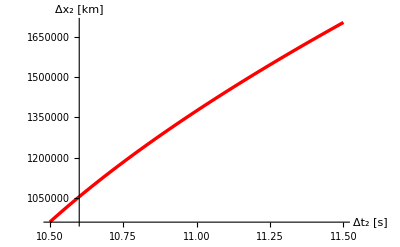

```mathematica
Plot[Δx2×10^-3/.r1[[2,1]],{Δt2,10.5,11.5},
TextStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
 PlotStyle->{{RGBColor[1,0,0],Thickness[0.006]}},
AxesLabel->{"Δt_2 [s]","Δx_2  [km]"}]
```

### Wyznaczenie zaleznosci predkosci rakiety od odleglosci czasoprzestrzennej dwoch wybuchow w ukladzie zwiazanym z rakieta poprzez rozwiazanie rownania bedacego matematycznym zapisem dylatacji czasu.

```mathematica
r2=Solve[Δt2==Δt1/(√(1-v^2/c^2)),v]
```

```mathematica
{{v->-(300000000 √(-100+Δt2^2))/Δt2},{v->(300000 √(-100+Δt2^2))/Δt2}}
```

### Sporzadzenie wykresu obrazujacego zaleznosc predkosci rakiety od odleglosci czasowej dwoch wybuchow na sloncu w ukladzie zwiazanym z rakieta.

```mathematica
Plot[v×10^6/.r2[[2,1]],{Δt2,0,1000},
TextStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
 PlotStyle->{{RGBColor[1,0,0],Thickness[0.006]}},
AxesLabel->{"Δt [s]","v  [km/s]"}]
```

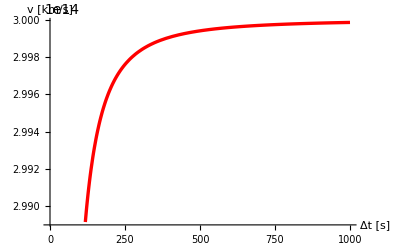

```mathematica
Plot[function,{var,min,max}]
```